```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap2D[];
sizes={64,64};
timeStep=0.001;
k=-0.3;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{64,64} | 2 | 4096 | {5,5} | {-5,-5} | {10/63,10/63} | {(63 π)/320,(63 π)/320} | {(63 π)/10,(63 π)/10}

time | energies | moments | misc
(0) | (total | 0.7
kinetic | 0.5
potential | 0.5
contact | -0.3
virial | -0.6) | (meanX | 0
meanY | 0
sigmaX | 0.707107
sigmaY | 0.707107
norm | 1.) | (steps | 0
A0 | 0.56414)

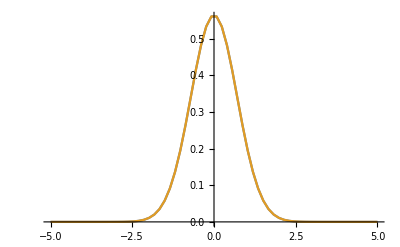

```mathematica
calcAllTable
p1=plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",30,10]]
```

{28.2221,Null}

time | energies | moments | misc
(30.) | (total | 0.616773
kinetic | 0.832394
potential | 0.309016
contact | -0.524636
virial | -0.00251667) | (meanX | 0
meanY | 0
sigmaX | 0.555892
sigmaY | 0.555892
norm | 1.) | (steps | 30000
A0 | 0.782022)

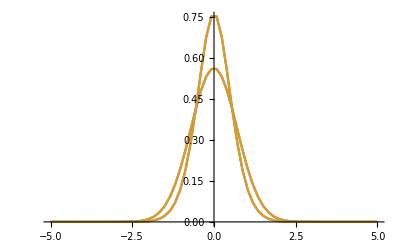

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->All]
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | 0.7 | 0.5 | 0.5 | -0.3 | -0.6
3. | 0.616791 | 0.827459 | 0.310803 | -0.521471 | -0.00963029
6. | 0.616773 | 0.832342 | 0.309034 | -0.524603 | -0.00259156
9. | 0.616773 | 0.832393 | 0.309016 | -0.524636 | -0.00251746
12. | 0.616773 | 0.832394 | 0.309016 | -0.524636 | -0.00251668
15. | 0.616773 | 0.832394 | 0.309016 | -0.524636 | -0.00251667
18. | 0.616773 | 0.832394 | 0.309016 | -0.524636 | -0.00251667
21. | 0.616773 | 0.832394 | 0.309016 | -0.524636 | -0.00251667
24. | 0.616773 | 0.832394 | 0.309016 | -0.524636 | -0.00251667
27. | 0.616773 | 0.832394 | 0.309016 | -0.524636 | -0.00251667
30. | 0.616773 | 0.832394 | 0.309016 | -0.524636 | -0.00251667

```mathematica
reportMoments
```

time | meanX | meanY | sigmaX | sigmaY | norm
0 | 0 | 0 | 0.707107 | 0.707107 | 1.
3. | 0 | 0 | 0.557497 | 0.557497 | 1.
6. | 0 | 0 | 0.555909 | 0.555909 | 1.
9. | 0 | 0 | 0.555892 | 0.555892 | 1.
12. | 0 | 0 | 0.555892 | 0.555892 | 1.
15. | 0 | 0 | 0.555892 | 0.555892 | 1.
18. | 0 | 0 | 0.555892 | 0.555892 | 1.
21. | 0 | 0 | 0.555892 | 0.555892 | 1.
24. | 0 | 0 | 0.555892 | 0.555892 | 1.
27. | 0 | 0 | 0.555892 | 0.555892 | 1.
30. | 0 | 0 | 0.555892 | 0.555892 | 1.